# Differential Geometry

## Stereographic projection

Animation

## (x,y) coordinates

```mathematica
Manipulate[Show[Plot3D[0,{x,-3,3},{y,-3,3},PlotRange->{{-3,3},{-3,3},{-1,1}},BoxRatios->{6,6,2},Mesh->None,PlotStyle->Opacity[0.7],ImageSize->Large,Boxed->False,Axes->False],Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ParametricPlot3D[{0+u(x),0+u(y),1+u(-1)},{u,0,5}],
ListPointPlot3D[{{x,y,0}},PlotStyle->{Thick,Red,PointSize[0.02]}],ListPointPlot3D[{{(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}},PlotStyle->{Blue,PointSize[0.02]}],ListPointPlot3D[{{0,0,1}},PlotStyle->{Black,PointSize[0.02]}]],{x,-3,3},{y,-3,3}]
```

## (x’,y’) coordinates

```mathematica
Manipulate[Show[Plot3D[0,{x,-3,3},{y,-3,3},PlotRange->{{-3,3},{-3,3},{-1,1}},BoxRatios->{6,6,2},Mesh->None,PlotStyle->Opacity[0.7],ImageSize->Large,Boxed->False,Axes->False],Graphics3D[{Opacity[0.5],Sphere[{0,0,0}]}],ParametricPlot3D[{0+u(x),0+u(y),-1+u(1)},{u,0,5}],
ListPointPlot3D[{{x,y,0}},PlotStyle->{Thick,Red,PointSize[0.02]}],ListPointPlot3D[{{(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),-1+2/(1+x^2+y^2)}},PlotStyle->{Thick,Blue,PointSize[0.02]}],ListPointPlot3D[{{0,0,-1}},PlotStyle->{Black,PointSize[0.02]}]],{x,-3,3},{y,-3,3}]
```

Sphere plot

```mathematica
Show[ParametricPlot3D[Table[{Sin[th]Cos[phi],Sin[th]Sin[phi],Cos[th]},{th,0,Pi/2,Pi/10}],{phi,0,2Pi},PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->False,Boxed->False],ParametricPlot3D[Table[{Sin[th]Cos[phi],Sin[th]Sin[phi],Cos[th]},{th,Pi/2,Pi,Pi/10}],{phi,0,2Pi},PlotStyle->Green],ParametricPlot3D[Table[{Sin[th]Cos[phi],Sin[th]Sin[phi],Cos[th]},{phi,0,2Pi,Pi/10}],{th,0,Pi},PlotStyle->Red],Graphics3D[Sphere[{0,0,0}]]]
```

-Graphics3D-

(x,y) coordinate plane

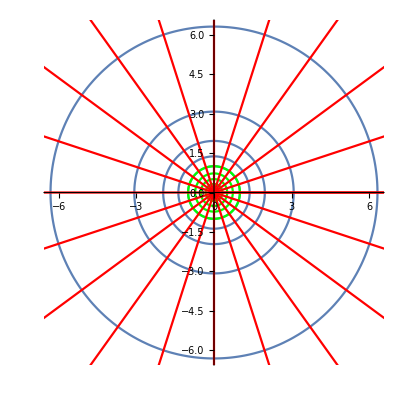

```mathematica
Show[ParametricPlot[Table[{(Sin[th]Cos[phi])/(1-Cos[th]),(Sin[th]Sin[phi])/(1-Cos[th])},{th,Pi/10,Pi/2,Pi/10}],{phi,0,2Pi}],ParametricPlot[Table[{(Sin[th]Cos[phi])/(1-Cos[th]),(Sin[th]Sin[phi])/(1-Cos[th])},{th,Pi/2,Pi,Pi/10}],{phi,0,2Pi},PlotStyle->Green],ParametricPlot[Table[{(Sin[th]Cos[phi])/(1-Cos[th]),(Sin[th]Sin[phi])/(1-Cos[th])},{phi,0,2Pi,Pi/10}],{th,0,Pi},PlotStyle->Red]]
```

(x’,y’) coordinate plane

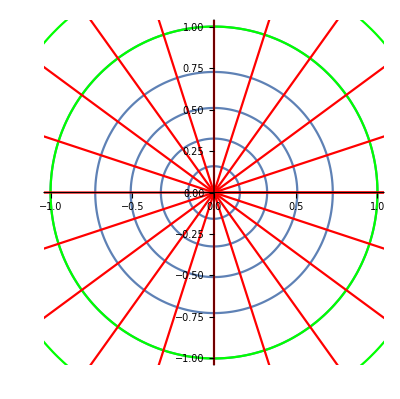

```mathematica
Show[ParametricPlot[Table[{(Sin[th]Cos[phi])/(1+Cos[th]),(Sin[th]Sin[phi])/(1+Cos[th])},{th,0,Pi/2,Pi/10}],{phi,0,2Pi}],ParametricPlot[Table[{(Sin[th]Cos[phi])/(1+Cos[th]),(Sin[th]Sin[phi])/(1+Cos[th])},{th,Pi/2,Pi-Pi/10,Pi/10}],{phi,0,2Pi},PlotStyle->Green],ParametricPlot[Table[{(Sin[th]Cos[phi])/(1+Cos[th]),(Sin[th]Sin[phi])/(1+Cos[th])},{phi,0,2Pi,Pi/10}],{th,0,Pi},PlotStyle->Red]]
```

Inverse map

(x,y)

```mathematica
Solve[x==X/(1-Z)&&y==Y/(1-Z)&&X^2+Y^2+Z^2==1,{X,Y,Z}]//FullSimplify
```

{{X→(2 x)/(1+x^2+y^2),Y→(2 y)/(1+x^2+y^2),Z→1-2/(1+x^2+y^2)}}

(x’,y’)

```mathematica
Solve[xx==X/(1+Z)&&yy==Y/(1+Z)&&X^2+Y^2+Z^2==1,{X,Y,Z}]//FullSimplify
```

{{X→(2 xx)/(1+xx^2+yy^2),Y→(2 yy)/(1+xx^2+yy^2),Z→-1+2/(1+xx^2+yy^2)}}

(x,y) gridlines on sphere:

```mathematica
Show[ParametricPlot3D[Table[({X,Y,Z}/.{X->(2 x)/(1+x^2+y^2),Y->(2 y)/(1+x^2+y^2),Z->1-2/(1+x^2+y^2)}),{y,-10,10}],{x,-10,10},PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->False,Boxed->False],ParametricPlot3D[Table[({X,Y,Z}/.{X->(2 x)/(1+x^2+y^2),Y->(2 y)/(1+x^2+y^2),Z->1-2/(1+x^2+y^2)}),{x,-10,10}],{y,-10,10},PlotStyle->Red],Graphics3D[Sphere[{0,0,0}]]]
```

-Graphics3D-

(x’,y’) gridlines on sphere:

```mathematica
Show[ParametricPlot3D[Table[({X,Y,Z}/.{X->(2 xx)/(1+xx^2+yy^2),Y->(2 yy)/(1+xx^2+yy^2),Z->-1+2/(1+xx^2+yy^2)}),{yy,-10,10}],{xx,-10,10},PlotRange->{{-1,1},{-1,1},{-1,1}},Axes->False,Boxed->False],ParametricPlot3D[Table[({X,Y,Z}/.{X->(2 xx)/(1+xx^2+yy^2),Y->(2 yy)/(1+xx^2+yy^2),Z->-1+2/(1+xx^2+yy^2)}),{xx,-10,10}],{yy,-10,10},PlotStyle->Red],Graphics3D[Sphere[{0,0,0}]]]
```

-Graphics3D-

## Curves

Sphere

```mathematica
Manipulate[Show[ParametricPlot3D[({(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->2 lam +1,y-> lam}),{lam,-1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False],Graphics3D[{Opacity[0.5],Sphere[]}],ListPointPlot3D[{{(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->2 u +1,y-> u}},PlotStyle->{Red,PointSize[0.03]}]],{u,-1,1}]
```

(x,y)

```mathematica
Manipulate[Show[ParametricPlot[{2 lam +1, lam},{lam,-1,1},PlotRange->{{-5,5},{-5,5}}],ListPlot[{{2 u +1, u}},PlotStyle->{Red,PointSize[0.03]}]],{u,-1,1}]
```

(x’,y’)

```mathematica
FullSimplify[{x/(x^2+y^2),y/(x^2+y^2)}/.{x->2 lam +1,y-> lam}]
```

{(1+2 lam)/(1+lam (4+5 lam)),lam/(1+lam (4+5 lam))}

```mathematica
{(1+2 lam)/(1+lam (4+5 lam)),lam/(1+lam (4+5 lam))}/.{lam->u}
```

{(1+2 u)/(1+u (4+5 u)),u/(1+u (4+5 u))}

```mathematica
Manipulate[Show[ParametricPlot[{(1+2 lam)/(1+lam (4+5 lam)),lam/(1+lam (4+5 lam))},{lam,-1,1},PlotRange->{{-5,5},{-5,5}}],ListPlot[{{(1+2 u)/(1+u (4+5 u)),u/(1+u (4+5 u))}},PlotStyle->{Red,PointSize[0.03]}]],{u,-1,1}]
```

## Tangent vectors

Sphere

```mathematica
Manipulate[Show[ParametricPlot3D[({(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->2 lam +1,y-> lam}),{lam,-1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False],ParametricPlot3D[({(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->2 lam +1-5 lam^3,y-> lam}),{lam,-1,1},PlotStyle->Darker[Blue]],Graphics3D[{Opacity[0.5],Sphere[]}],ListPointPlot3D[{{(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->2 u +1,y-> u}},PlotStyle->{Red,PointSize[0.03]}],ListPointPlot3D[{{(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->2 u +1-5 u^3,y-> u}},PlotStyle->{Red,PointSize[0.03]}]],{u,-1,1}]
```

(x,y)

```mathematica
Manipulate[Show[ParametricPlot[{2 lam +1, lam},{lam,-1,1},PlotRange->{{-5,5},{-5,5}}],ParametricPlot[{2 lam +1-5 lam^3, lam},{lam,-1,1},PlotStyle->Darker[Blue]],ListPlot[{{2 u +1, u}},PlotStyle->{Red,PointSize[0.03]}],ListPlot[{{2 u +1-5 u^3, u}},PlotStyle->{Red,PointSize[0.03]}]],{u,-1,1}]
```

(x’,y’)

```mathematica
FullSimplify[{x/(x^2+y^2),y/(x^2+y^2)}/.{x->2 lam +1-5 lam^3,y-> lam}]
```

{(1+2 lam-5 lam^3)/(lam^2+(1+2 lam-5 lam^3)^2),lam/(lam^2+(1+2 lam-5 lam^3)^2)}

```mathematica
{(1+2 lam-5 lam^3)/(lam^2+(1+2 lam-5 lam^3)^2),lam/(lam^2+(1+2 lam-5 lam^3)^2)}/.{lam->u}
```

{(1+2 u-5 u^3)/(u^2+(1+2 u-5 u^3)^2),u/(u^2+(1+2 u-5 u^3)^2)}

```mathematica
Manipulate[Show[ParametricPlot[{(1+2 lam)/(1+lam (4+5 lam)),lam/(1+lam (4+5 lam))},{lam,-1,1},PlotRange->{{-5,5},{-5,5}}],ParametricPlot[{(1+2 lam-5 lam^3)/(lam^2+(1+2 lam-5 lam^3)^2),lam/(lam^2+(1+2 lam-5 lam^3)^2)},{lam,-1,1},PlotStyle->Darker[Blue]],ListPlot[{{(1+2 u)/(1+u (4+5 u)),u/(1+u (4+5 u))}},PlotStyle->{Red,PointSize[0.03]}],ListPlot[{{(1+2 u-5 u^3)/(u^2+(1+2 u-5 u^3)^2),u/(u^2+(1+2 u-5 u^3)^2)}},PlotStyle->{Red,PointSize[0.03]}]],{u,-1,1}]
```

```mathematica
D[x/(x^2+y^2),x]//FullSimplify
```

(-x^2+y^2)/((x^2+y^2)^2)

```mathematica
D[x/(x^2+y^2),y]//FullSimplify
```

-(2 x y)/((x^2+y^2)^2)

## Basis vectors using (x,y) coordinates

(x,y)

```mathematica
xLinePlot=ParametricPlot[{lam +1, 0},{lam,-5,5},PlotRange->{{-5,5},{-5,5}},PlotStyle->Red];
xLinePlotForArrow=ParametricPlot[{lam +1, 0},{lam,-4,4},PlotStyle->Red];
yLinePlot=ParametricPlot[{1, lam},{lam,-5,5},PlotRange->{{-5,5},{-5,5}},PlotStyle->Darker[Blue]];
yLinePlotForArrow=ParametricPlot[{1, lam},{lam,-4,4},PlotStyle->Darker[Blue]];
```

```mathematica
xLinePlotForArrow[[1,1,3,1,2]]
```

Line[{{-3.,0.},{-2.99755,0.},{-2.99509,0.},{-2.99019,0.},{-2.98037,0.},{-2.96074,0.},{-2.92149,0.},{-2.84297,0.},{-2.67273,0.},{-2.51378,0.},{-2.35794,0.},{-2.18889,0.},{-2.03113,0.},{-1.86015,0.},{-1.6923,0.},{-1.53572,0.},{-1.36594,0.},{-1.20744,0.},{-1.05206,0.},{-0.883465,0.},{-0.726155,0.},{-0.555636,0.},{-0.388235,0.},{-0.232116,0.},{-0.0627884,0.},{0.095258,0.},{0.266513,0.},{0.43465,0.},{0.591505,0.},{0.761569,0.},{0.920351,0.},{1.07602,0.},{1.24489,0.},{1.40248,0.},{1.57328,0.},{1.74096,0.},{1.89736,0.},{2.06697,0.},{2.2253,0.},{2.38051,0.},{2.54893,0.},{2.70606,0.},{2.87641,0.},{3.03547,0.},{3.19142,0.},{3.36057,0.},{3.51844,0.},{3.68952,0.},{3.85749,0.},{4.01417,0.},{4.18406,0.},{4.34267,0.},{4.49816,0.},{4.66686,0.},{4.82427,0.},{4.82702,0.},{4.82977,0.},{4.83526,0.},{4.84624,0.},{4.86821,0.},{4.91214,0.},{4.91488,0.},{4.91763,0.},{4.92312,0.},{4.9341,0.},{4.95607,0.},{4.95881,0.},{4.96156,0.},{4.96705,0.},{4.97803,0.},{4.98078,0.},{4.98353,0.},{4.98902,0.},{4.99176,0.},{4.99451,0.},{4.99725,0.},{5.,0.}}]

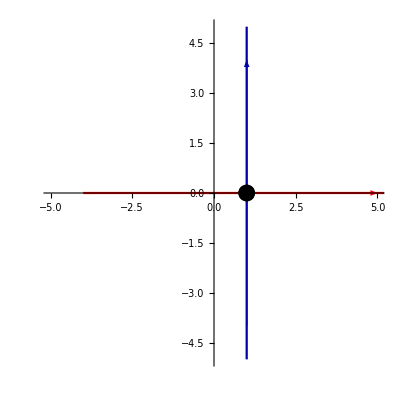

```mathematica
Show[xLinePlot,Graphics[{Red,Arrow[xLinePlotForArrow[[1,1,3,1,2]]]}],yLinePlot,Graphics[{Darker[Blue],Arrow[yLinePlotForArrow[[1,1,3,1,2]]]}],ListPlot[{{1,0}},PlotStyle->{Black,PointSize[0.03]}]]
```

Sphere

```mathematica
xLinePlot=ParametricPlot3D[({(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x-> lam +1,y->0}),{lam,-5,5},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False,PlotStyle->Red];
yLinePlot=ParametricPlot3D[({(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->1,y-> lam}),{lam,-5,5},PlotStyle->Darker[Blue]];
```

```mathematica
Show[Graphics3D[{Red,Thick,Arrow[xLinePlot[[1,1,3,1,3]]]},Boxed->False],Graphics3D[{Darker[Blue],Thick,Arrow[yLinePlot[[1,1,3,1,3]]]}],Graphics3D[{Opacity[0.5],Sphere[]}],ListPointPlot3D[{{1,0,0}},PlotStyle->{Black,PointSize[0.03]}]]
```

-Graphics3D-

(x’,y’)

```mathematica
FullSimplify[{x/(x^2+y^2),y/(x^2+y^2)}/.{x->lam +1,y-> 0}]
FullSimplify[{x/(x^2+y^2),y/(x^2+y^2)}/.{x->1,y->lam}]
```

{1/(1+lam),0}

{1/(1+lam^2),lam/(1+lam^2)}

```mathematica
xLinePlot=ParametricPlot[{1/(1+lam),0},{lam,-5,5},PlotRange->{{-5,5},{-5,5}},PlotStyle->Red];
xLinePlotForArrow=ParametricPlot[{1/(1+lam),0},{lam,-4,4},PlotStyle->Red];
yLinePlot=ParametricPlot[{1/(1+lam^2),lam/(1+lam^2)},{lam,-5,5},PlotRange->{{-5,5},{-5,5}},PlotStyle->Darker[Blue]];
yLinePlotForArrow=ParametricPlot[{1/(1+lam^2),lam/(1+lam^2)},{lam,-4,4},PlotStyle->Darker[Blue]];
```

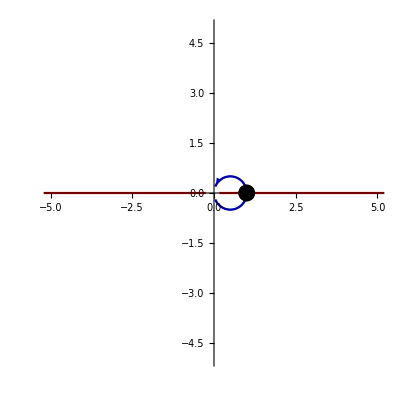

```mathematica
Show[xLinePlot,Graphics[{Red,Arrow[xLinePlotForArrow[[1,1,3,1,2]]]}],yLinePlot,Graphics[{Darker[Blue],Arrow[yLinePlotForArrow[[1,1,3,1,2]]]}],ListPlot[{{1,0}},PlotStyle->{Black,PointSize[0.03]}]]
```

## Transition Matrix

```mathematica
transitionMatrix=Join[{D[{x/(x^2+y^2),y/(x^2+y^2)},x]},{D[{x/(x^2+y^2),y/(x^2+y^2)},y]}]//FullSimplify
```

{{(-x^2+y^2)/((x^2+y^2)^2),-(2 x y)/((x^2+y^2)^2)},{-(2 x y)/((x^2+y^2)^2),((x-y) (x+y))/((x^2+y^2)^2)}}

## Vector field

Specify vector field in (x,y) coordinates:

```mathematica
vecFieldFunc[x_,y_]:={x+y,x}
```

Components in (x’,y’) coordinates:

```mathematica
FullSimplify[transitionMatrix.vecFieldFunc[x,y]/.{x->xx/(xx^2+yy^2),y->yy/(xx^2+yy^2)}]
```

{xx+yy-(2 xx^2 (xx+2 yy))/(xx^2+yy^2),(xx (xx-3 yy) (xx+yy))/(xx^2+yy^2)}

```mathematica
arrowFromPoint[x0_,y0_,u_]:={x0,y0}+u vecFieldFunc[x0,y0]
```

```mathematica
arrowFromPointOtherCoords[x0_,y0_,u_]:= {x/(x^2+y^2),y/(x^2+y^2)}/.{x->x0+u vecFieldFunc[x0,y0][[1]],y->y0+u vecFieldFunc[x0,y0][[2]]}
```

```mathematica
arrowFromPointSphere[x0_,y0_,u_]:={(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)}/.{x->x0+u vecFieldFunc[x0,y0][[1]],y->y0+u vecFieldFunc[x0,y0][[2]]}
```

Plot vector field in (x,y) coordinates

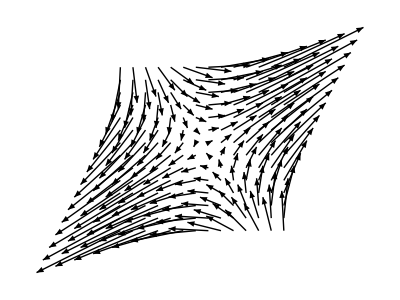

```mathematica
Show[Table[Graphics[Arrow[Table[arrowFromPoint[x0,y0,u],{u,0,0.5,0.05}]]],{x0,-2,2,0.3},{y0,-2,2,0.3}]]
```

Plot vector field in (x’,y’) coordinates:

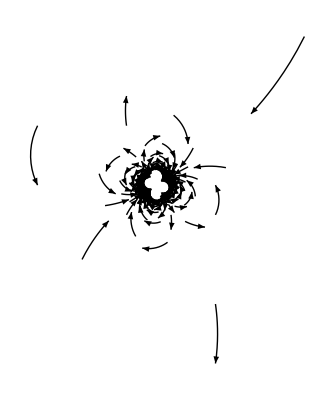

```mathematica
Show[Table[Graphics[Arrow[Table[arrowFromPointOtherCoords[x0,y0,u],{u,0,0.5,0.05}]]],{x0,-2,2,0.3},{y0,-2,2,0.3}]]
```

Plot vector field on sphere:

```mathematica
Show[Table[Graphics3D[Arrow[Table[arrowFromPointSphere[x0,y0,u],{u,0,0.5,0.05}]]],{x0,-2,2,0.3},{y0,-2,2,0.3}]]
```

-Graphics3D-

## Covectors

```mathematica
(1-2/(1+x^2+y^2))/.{x->1,y->0}
```

0

```mathematica
{D[(1-2/(1+x^2+y^2)),x],D[(1-2/(1+x^2+y^2)),y]}/.{x->1,y->0}
```

{1,0}

```mathematica
{D[(-1+2/(1+xx^2+yy^2)),xx],D[(-1+2/(1+xx^2+yy^2)),yy]}/.{xx->1,yy->0}
```

{-1,0}

```mathematica
{D[(1-2/(1+x^2+y^2))+10,x],D[(1-2/(1+x^2+y^2))+10,y]}/.{x->1,y->0}
```

{1,0}

```mathematica
FullSimplify[((1-2/(1+x^2+y^2))+10)/.{x->xx/(xx^2+yy^2),y->yy/(xx^2+yy^2)}]
```

9+2/(1+xx^2+yy^2)

```mathematica
{D[(9+2/(1+xx^2+yy^2)),xx],D[(9+2/(1+xx^2+yy^2)),yy]}/.{xx->1,yy->0}
```

{-1,0}

## Metric

In (x,y) coordinates

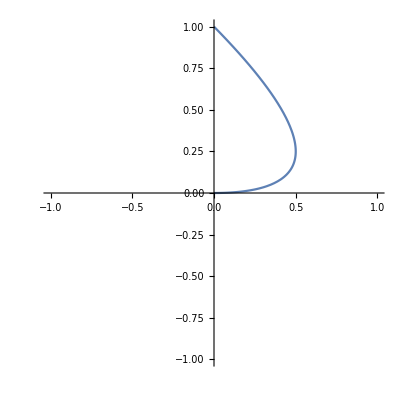

```mathematica
ParametricPlot[{2 u+1-2 u^2-1,u^2},{u,0,1},PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
D[{2 u+1-2 u^2-1,u^2},u]
```

{2-4 u,2 u}

```mathematica
{2-4 u,2 u}.{2-4 u,2 u}
```

(2-4 u)^2+4 u^2

```mathematica
Integrate[Sqrt[(2-4 u)^2+4 u^2],u]//FullSimplify
```

1/25 (5 (-2+5 u) √(1+u (-4+5 u))-√5 ArcSinh[2-5 u])

```mathematica
len=FullSimplify[((1/25 (5 (-2+5 u) √(1+u (-4+5 u))-√5 ArcSinh[2-5 u]))/.u->1)-((1/25 (5 (-2+5 u) √(1+u (-4+5 u))-√5 ArcSinh[2-5 u]))/.u->0)]
```

1/25 (10+15 √2+√5 ArcSinh[2]+√5 ArcSinh[3])

```mathematica
len//N
```

1.5403

Plot curve in polar coordinates:

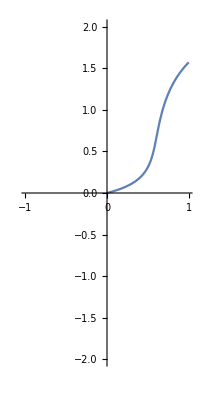

```mathematica
ParametricPlot[{Sqrt[x^2+y^2],ArcTan[y/x]}/.{x->2 u+1-2 u^2-1,y->u^2},{u,0,1},PlotRange->{{-1,1},{-2,2}}]
```

```mathematica
FullSimplify[Expand[(Cos[th]dr-r Sin[th]dth)^2+(Sin[th] dr+r Cos[th] dth)^2]]
```

dr^2+dth^2 r^2

```mathematica
D[{(2 x)/(1+x^2+y^2),(2 y)/(1+x^2+y^2),1-2/(1+x^2+y^2)},x]
```

{-(4 x^2)/((1+x^2+y^2)^2)+2/(1+x^2+y^2),-(4 x y)/((1+x^2+y^2)^2),(4 x)/((1+x^2+y^2)^2)}

```mathematica
FullSimplify[Expand[(D[(2 x)/(1+x^2+y^2),x]dx+D[(2 x)/(1+x^2+y^2),y]dy)^2+(D[(2 y)/(1+x^2+y^2),x]dx+D[(2 y)/(1+x^2+y^2),y]dy)^2+(D[1-2/(1+x^2+y^2),x]dx+D[1-2/(1+x^2+y^2),y]dy)^2]]
```

(4 (dx^2+dy^2))/((1+x^2+y^2)^2)